# Notebook for : Exact Spacetimes in Einstein’s General Relativity by Griffiths and Podolsky Chapter 5: Anti de Sitter

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
March 27, 2022

```mathematica
(* Problem with the symbolize - need it for dtReplace to work... *)
```

```mathematica
(* 
Do figure 5.7
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book

```mathematica
Hyperlink["Exact Space-Times in Einstein's General Relativity",
"https://www.cambridge.org/core/books/exact-spacetimes-in-einsteins-general-relativity/48896A8900897F53BDAA917456E884D6"]
```

[Exact Space-Times in Einstein's General Relativity](https://www.cambridge.org/core/books/exact-spacetimes-in-einsteins-general-relativity/48896A8900897F53BDAA917456E884D6)

```mathematica
Hyperlink["Exact Space-Times in Einstein's General Relativity Front Matter",
"https://assets.cambridge.org/97805218/89278/frontmatter/9780521889278_frontmatter.pdf"]
```

[Exact Space-Times in Einstein's General Relativity Front Matter](https://assets.cambridge.org/97805218/89278/frontmatter/9780521889278_frontmatter.pdf)

```mathematica
Hyperlink["Understanding Exact Spacetimes CQG plus",
"https://cqgplus.com/2018/08/20/understanding-exact-space-times/"]
```

[Understanding Exact Spacetimes CQG plus](https://cqgplus.com/2018/08/20/understanding-exact-space-times/)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 6 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[Z, 0]]
Symbolize[Subscript[Z, 1]]
Symbolize[Subscript[Z, 2]]
Symbolize[Subscript[Z, 3]]
Symbolize[Subscript[Z, 4]]
Symbolize[Subscript[η, 0]]
Symbolize[Subscript[R, 0]]
Symbolize[Subscript[t, -1]]
Symbolize[Subscript[t, b]]
Symbolize[Subscript[z, b]]
Symbolize[Subscript[t, k]]
Symbolize[Subscript[z, k]]
```

```mathematica
CreatePalette[{ 
PasteButton[Subscript[Z, 0]],
 PasteButton[Subscript[Z, 1]] , 
PasteButton[Subscript[Z, 2]] ,
PasteButton[Subscript[Z, 3]] ,
PasteButton[Subscript[Z, 4]] ,
PasteButton[Subscript[R, 0]],
PasteButton[Subscript[η, 0]]
}]
```

rzudu_shm46FrontEndObject[LinkObject["rzudu_shm", 3, 1]]46Untitled-4

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[Subscript[Z, 0]] -> Subscript[dZ, 0] ,
Dt[Subscript[Z, 1]] -> Subscript[dZ, 1] ,
Dt[Subscript[Z, 2]]-> Subscript[dZ, 2] ,
Dt[Subscript[Z, 3]]-> Subscript[dZ, 3] ,
Dt[Subscript[Z, 4]] -> Subscript[dZ, 4] ,
Dt[Subscript[η, 0]]-> Subscript[dη, 0] , 
Dt[Subscript[t, -1]]-> Subscript[dt, -1] , 
Dt[Subscript[t, b]]-> Subscript[dt, b] , 
Dt[Subscript[z, b]]-> Subscript[dz, b] , 
Dt[Subscript[t, k]]-> Subscript[dt, k] , 
Dt[Subscript[z, k]]-> Subscript[dz, k] , 
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z] -> dz , 
Dt[r]-> dr , 
Dt[s]-> ds , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[𝓍]-> d𝓍 ,  
 Dt[z]-> dz , 
 Dt[ψ]-> dψ , 
Dt[τ]-> dτ , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[R]-> dR, 
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[X]-> dX , 
Dt[Y]-> dY , 
Dt[Z]-> dZ , 
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ , 
Dt[ζ]-> dζ , 
Dt[ζbar]-> dζbar 
};
dtReplace // TableForm
```

Dt[Z_0]→dZ_0
Dt[Z_1]→dZ_1
Dt[Z_2]→dZ_2
Dt[Z_3]→dZ_3
Dt[Z_4]→dZ_4
Dt[η_0]→dη_0
Dt[t_-1]→dt_-1
Dt[t_b]→dt_b
Dt[z_b]→dz_b
Dt[t_k]→dt_k
Dt[z_k]→dz_k
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[r]→dr
Dt[s]→ds
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[𝓍]→d𝓍
Dt[z]→dz
Dt[ψ]→dψ
Dt[τ]→dτ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[R]→dR
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ
Dt[ζ]→dζ
Dt[ζbar]→dζbar

```mathematica
Subscript[R, 0]/:Dt[Subscript[R, 0]]=0  ; (* Subscript[R, 0] is a constant, it's differential is zero *) 
M/:Dt[M]=0  ;   (*  we use M for mass and reserve m for a null vector *)
𝒞 /:Dt[𝒞]= 0 ; (* Regular C is protected use [esc]scC[esc].  See 3.12 *)
a /:Dt[a]= 0 ;   (* 3.13 *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 5.2: Anti de Sitter Hyperboloid

```mathematica
Clear[eq5pt1]
eq5pt1 = 
- Subscript[Z, 0]^2+ Subscript[Z, 1]^2+Subscript[Z, 2]^2+Subscript[Z, 3]^2-Subscript[Z, 4]^2== - a^2
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

```mathematica
Clear[eq5pt1a]
eq5pt1a = 
a^2 == -3/Λ
```

a^2==-3/Λ

```mathematica
Clear[eq5pt2]
eq5pt2 = 
 - Subscript[dZ, 0]^2 + Subscript[dZ, 1]^2 + Subscript[dZ, 2]^2 + Subscript[dZ, 3]^2- Subscript[dZ, 4]^2
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2-dZ_4^2

```mathematica
Clear[metric5pt2]
metric5pt2 = 
lineToMetric[ eq5pt2 ,{Subscript[dZ, 0],Subscript[dZ, 1],Subscript[dZ, 2],Subscript[dZ, 3],Subscript[dZ, 4]}] ;
metric5pt2  // MatrixForm
```

(-1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -1)

## Line Element and Metric 5.4: Anti de Sitter in Global Coordinates

```mathematica
Clear[eq5pt3]
eq5pt3 = { 
Subscript[Z, 0] ==  a Cosh[r] Sin[T/a] ,
Subscript[Z, 1] ==  a Sinh[r] Cos[θ] ,
Subscript[Z, 2] ==  a Sinh[r] Sin[θ] Cos[ϕ] ,
Subscript[Z, 3] ==  a Sinh[r] Sin[θ] Sin[ϕ] , 
Subscript[Z, 4] ==  a Cosh[r] Cos[T/a] 
} ;
( eq5pt3  /. Equal-> Rule  ) // TableForm
```

Z_0→a Cosh[r] Sin[T/a]
Z_1→a Cos[θ] Sinh[r]
Z_2→a Cos[ϕ] Sin[θ] Sinh[r]
Z_3→a Sin[θ] Sin[ϕ] Sinh[r]
Z_4→a Cos[T/a] Cosh[r]

```mathematica
(* Just a quick check to make sure our transformations are correct *) 

eq5pt1
eq5pt1 /. ( eq5pt3  /. Equal-> Rule  )
eq5pt1 /. ( eq5pt3  /. Equal-> Rule  ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

-a^2 Cos[T/a]^2 Cosh[r]^2-a^2 Cosh[r]^2 Sin[T/a]^2+a^2 Cos[θ]^2 Sinh[r]^2+a^2 Cos[ϕ]^2 Sin[θ]^2 Sinh[r]^2+a^2 Sin[θ]^2 Sin[ϕ]^2 Sinh[r]^2==-a^2

True

```mathematica
Dt[ ( eq5pt3  /. Equal-> Rule  )] /. dtReplace // TableForm
```

dZ_0→dT Cos[T/a] Cosh[r]+a dr Sin[T/a] Sinh[r]
dZ_1→a dr Cos[θ] Cosh[r]-a dθ Sin[θ] Sinh[r]
dZ_2→a dr Cos[ϕ] Cosh[r] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Sinh[r]-a dϕ Sin[θ] Sin[ϕ] Sinh[r]
dZ_3→a dr Cosh[r] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Sin[θ] Sinh[r]+a dθ Cos[θ] Sin[ϕ] Sinh[r]
dZ_4→-dT Cosh[r] Sin[T/a]+a dr Cos[T/a] Sinh[r]

```mathematica
eq5pt2
eq5pt2 /. (Dt[ ( eq5pt3  /. Equal-> Rule  )] /. dtReplace  )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2-dZ_4^2

-(-dT Cosh[r] Sin[T/a]+a dr Cos[T/a] Sinh[r])^2-(dT Cos[T/a] Cosh[r]+a dr Sin[T/a] Sinh[r])^2+(a dr Cos[θ] Cosh[r]-a dθ Sin[θ] Sinh[r])^2+(a dr Cosh[r] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Sin[θ] Sinh[r]+a dθ Cos[θ] Sin[ϕ] Sinh[r])^2+(a dr Cos[ϕ] Cosh[r] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Sinh[r]-a dϕ Sin[θ] Sin[ϕ] Sinh[r])^2

```mathematica
Clear[metric5pt4]
metric5pt4 = 
lineToMetric[ (eq5pt2 /. (Dt[ ( eq5pt3  /. Equal-> Rule  )] /. dtReplace  ) ), {dT,dr,dθ,dϕ}] // Expand // Simplify  ;
metric5pt4 // MatrixForm
```

(-Cosh[r]^2 | 0 | 0 | 0
0 | a^2 | 0 | 0
0 | 0 | a^2 Sinh[r]^2 | 0
0 | 0 | 0 | a^2 Sin[θ]^2 Sinh[r]^2)

```mathematica
Clear[eq5pt4]
eq5pt4 = 
Collect[ metricToLine[metric5pt4 , {dT,dr,dθ,dϕ} ] , { a^2 Sinh[r]^2} ]
```

a^2 dr^2-dT^2 Cosh[r]^2+a^2 (dθ^2+dϕ^2 Sin[θ]^2) Sinh[r]^2

```mathematica
Clear[fig5pt1]
fig5pt1 = 
eq5pt1 /. Subscript[Z, 2]-> 0  /. Subscript[Z, 3]-> 0   /. a -> 1
```

-Z_0^2+Z_1^2-Z_4^2==-1

```mathematica
ContourPlot3D[ Evaluate[fig5pt1] , { Subscript[Z, 0] , -10 , 10 } , { Subscript[Z, 1] , -10 , 10 } , { Subscript[Z, 4] , -10 , 10 },MeshFunctions->{#1^2-#2^2&,#1^2+#3^2&} , AxesLabel->{Z0 ,Z1 ,Z4 }]
```

-Graphics3D-

## Line Element and Metric 5.6: Anti de Sitter Static Spherically Symmetric

```mathematica
Clear[eq5pt5]
eq5pt5 = { 
Subscript[Z, 0] ==  √(a^2+R^2)Sin[T/a] ,
Subscript[Z, 1] ==  R Cos[θ] ,
Subscript[Z, 2] ==  R Sin[θ] Cos[ϕ] ,
Subscript[Z, 3] ==  R Sin[θ] Sin[ϕ] ,
Subscript[Z, 4] ==  √(a^2+R^2)Cos[T/a]
} ;
( eq5pt5  /. Equal-> Rule )   // TableForm
```

Z_0→√(a^2+R^2) Sin[T/a]
Z_1→R Cos[θ]
Z_2→R Cos[ϕ] Sin[θ]
Z_3→R Sin[θ] Sin[ϕ]
Z_4→√(a^2+R^2) Cos[T/a]

```mathematica
(* Just a quick check to make sure our transformations are correct *) 

eq5pt1
eq5pt1 /. ( eq5pt5  /. Equal-> Rule )
eq5pt1 /. ( eq5pt5  /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

-((a^2+R^2) Cos[T/a]^2)+R^2 Cos[θ]^2-(a^2+R^2) Sin[T/a]^2+R^2 Cos[ϕ]^2 Sin[θ]^2+R^2 Sin[θ]^2 Sin[ϕ]^2==-a^2

True

```mathematica
( Dt[( eq5pt5  /. Equal-> Rule )] /. dtReplace  ) // TableForm
```

dZ_0→(dT √(a^2+R^2) Cos[T/a])/a+(dR R Sin[T/a])/(√(a^2+R^2))
dZ_1→dR Cos[θ]-dθ R Sin[θ]
dZ_2→dθ R Cos[θ] Cos[ϕ]+dR Cos[ϕ] Sin[θ]-dϕ R Sin[θ] Sin[ϕ]
dZ_3→dϕ R Cos[ϕ] Sin[θ]+dθ R Cos[θ] Sin[ϕ]+dR Sin[θ] Sin[ϕ]
dZ_4→(dR R Cos[T/a])/(√(a^2+R^2))-(dT √(a^2+R^2) Sin[T/a])/a

```mathematica
eq5pt2
eq5pt2 /. ( Dt[( eq5pt5  /. Equal-> Rule )] /. dtReplace  )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2-dZ_4^2

-((dT √(a^2+R^2) Cos[T/a])/a+(dR R Sin[T/a])/(√(a^2+R^2)))^2-((dR R Cos[T/a])/(√(a^2+R^2))-(dT √(a^2+R^2) Sin[T/a])/a)^2+(dR Cos[θ]-dθ R Sin[θ])^2+(dϕ R Cos[ϕ] Sin[θ]+dθ R Cos[θ] Sin[ϕ]+dR Sin[θ] Sin[ϕ])^2+(dθ R Cos[θ] Cos[ϕ]+dR Cos[ϕ] Sin[θ]-dϕ R Sin[θ] Sin[ϕ])^2

```mathematica
Clear[metric5pt6]
metric5pt6 = 
lineToMetric[ (eq5pt2 /. ( Dt[( eq5pt5  /. Equal-> Rule )] /. dtReplace  ) ) , {dT,dR,dθ,dϕ}] // Expand // Simplify  ;
metric5pt6 // MatrixForm
```

(-1-R^2/a^2 | 0 | 0 | 0
0 | a^2/(a^2+R^2) | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[θ]^2)

```mathematica
(* Do rest by hand *) 

 Clear[eq5pt6]
eq5pt6 = 
metricToLine[metric5pt6 , {dT,dR,dθ,dϕ}  ]
```

dθ^2 R^2+(a^2 dR^2)/(a^2+R^2)+dT^2 (-1-R^2/a^2)+dϕ^2 R^2 Sin[θ]^2

## Line Element and Metric 5.8: Anti de Sitter Poincare Ball

```mathematica
Clear[eq5pt7]
eq5pt7 = { 
Subscript[Z, 0] ==  a((1+ψ^2)/(1-ψ^2)) Sin[T/a] ,
Subscript[Z, 1] ==  a((2 ψ)/(1-ψ^2))Cos[θ] , 
Subscript[Z, 2] ==  a((2 ψ)/(1-ψ^2))Sin[θ] Cos[ϕ] ,
Subscript[Z, 3] ==   a((2 ψ)/(1-ψ^2))Sin[θ] Sin[ϕ] , 
Subscript[Z, 4] ==    a((1+ψ^2)/(1-ψ^2)) Cos[T/a]
} ;
( eq5pt7 /. Equal-> Rule )   // TableForm
```

Z_0→(a (1+ψ^2) Sin[T/a])/(1-ψ^2)
Z_1→(2 a ψ Cos[θ])/(1-ψ^2)
Z_2→(2 a ψ Cos[ϕ] Sin[θ])/(1-ψ^2)
Z_3→(2 a ψ Sin[θ] Sin[ϕ])/(1-ψ^2)
Z_4→(a (1+ψ^2) Cos[T/a])/(1-ψ^2)

```mathematica
(* Just a quick check to make sure our transformations are correct *) 

eq5pt1
eq5pt1 /. ( eq5pt7 /. Equal-> Rule )
eq5pt1 /. ( eq5pt7 /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

-(a^2 (1+ψ^2)^2 Cos[T/a]^2)/((1-ψ^2)^2)+(4 a^2 ψ^2 Cos[θ]^2)/((1-ψ^2)^2)-(a^2 (1+ψ^2)^2 Sin[T/a]^2)/((1-ψ^2)^2)+(4 a^2 ψ^2 Cos[ϕ]^2 Sin[θ]^2)/((1-ψ^2)^2)+(4 a^2 ψ^2 Sin[θ]^2 Sin[ϕ]^2)/((1-ψ^2)^2)==-a^2

True

```mathematica
( Dt[eq5pt7/. Equal-> Rule ]  /. dtReplace )  // TableForm
```

dZ_0→(dT (1+ψ^2) Cos[T/a])/(1-ψ^2)+(2 a dψ ψ Sin[T/a])/(1-ψ^2)+(2 a dψ ψ (1+ψ^2) Sin[T/a])/((1-ψ^2)^2)
dZ_1→(4 a dψ ψ^2 Cos[θ])/((1-ψ^2)^2)+(2 a dψ Cos[θ])/(1-ψ^2)-(2 a dθ ψ Sin[θ])/(1-ψ^2)
dZ_2→(2 a dθ ψ Cos[θ] Cos[ϕ])/(1-ψ^2)+(4 a dψ ψ^2 Cos[ϕ] Sin[θ])/((1-ψ^2)^2)+(2 a dψ Cos[ϕ] Sin[θ])/(1-ψ^2)-(2 a dϕ ψ Sin[θ] Sin[ϕ])/(1-ψ^2)
dZ_3→(2 a dϕ ψ Cos[ϕ] Sin[θ])/(1-ψ^2)+(2 a dθ ψ Cos[θ] Sin[ϕ])/(1-ψ^2)+(4 a dψ ψ^2 Sin[θ] Sin[ϕ])/((1-ψ^2)^2)+(2 a dψ Sin[θ] Sin[ϕ])/(1-ψ^2)
dZ_4→(2 a dψ ψ Cos[T/a])/(1-ψ^2)+(2 a dψ ψ (1+ψ^2) Cos[T/a])/((1-ψ^2)^2)-(dT (1+ψ^2) Sin[T/a])/(1-ψ^2)

```mathematica
eq5pt2
eq5pt2 /. ( Dt[eq5pt7/. Equal-> Rule ]  /. dtReplace )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2-dZ_4^2

-((dT (1+ψ^2) Cos[T/a])/(1-ψ^2)+(2 a dψ ψ Sin[T/a])/(1-ψ^2)+(2 a dψ ψ (1+ψ^2) Sin[T/a])/((1-ψ^2)^2))^2-((2 a dψ ψ Cos[T/a])/(1-ψ^2)+(2 a dψ ψ (1+ψ^2) Cos[T/a])/((1-ψ^2)^2)-(dT (1+ψ^2) Sin[T/a])/(1-ψ^2))^2+((4 a dψ ψ^2 Cos[θ])/((1-ψ^2)^2)+(2 a dψ Cos[θ])/(1-ψ^2)-(2 a dθ ψ Sin[θ])/(1-ψ^2))^2+((2 a dϕ ψ Cos[ϕ] Sin[θ])/(1-ψ^2)+(2 a dθ ψ Cos[θ] Sin[ϕ])/(1-ψ^2)+(4 a dψ ψ^2 Sin[θ] Sin[ϕ])/((1-ψ^2)^2)+(2 a dψ Sin[θ] Sin[ϕ])/(1-ψ^2))^2+((2 a dθ ψ Cos[θ] Cos[ϕ])/(1-ψ^2)+(4 a dψ ψ^2 Cos[ϕ] Sin[θ])/((1-ψ^2)^2)+(2 a dψ Cos[ϕ] Sin[θ])/(1-ψ^2)-(2 a dϕ ψ Sin[θ] Sin[ϕ])/(1-ψ^2))^2

```mathematica
Clear[metric5pt8]
metric5pt8 = 
lineToMetric[( eq5pt2 /. ( Dt[eq5pt7/. Equal-> Rule ]  /. dtReplace )) , {dT,dψ,dθ,dϕ}] // Expand // Simplify  ;
metric5pt8 // MatrixForm
```

(-((1+ψ^2)^2)/((-1+ψ^2)^2) | 0 | 0 | 0
0 | (4 a^2)/((-1+ψ^2)^2) | 0 | 0
0 | 0 | (4 a^2 ψ^2)/((-1+ψ^2)^2) | 0
0 | 0 | 0 | (4 a^2 ψ^2 Sin[θ]^2)/((-1+ψ^2)^2))

```mathematica
Clear[eq5pt8]
eq5pt8 = 
Collect[ metricToLine[metric5pt8,{dT,dψ,dθ,dϕ}] ,(4 a^2)/((-1+ψ^2)^2)] ;
eq5pt8 // pdConv
```

(4 a^2 (dθ^2 ψ^2+dψ^2+dϕ^2 ψ^2 sin^2(θ)))/((ψ^2-1)^2)-(dT^2 (ψ^2+1)^2)/((ψ^2-1)^2)

## Line Element and Metric 5.10: Anti de Sitter Conformal to Einstein Static

```mathematica
Clear[eq5pt9]
eq5pt9 = {
 Tan[χ]== Sinh[r],
η == T/a
} ;
eq5pt9  // TableForm
```

Tan[χ]==Sinh[r]
η==T/a

```mathematica
( Solve[eq5pt9 ,{r,T}][[2]] /. C[1]-> 0  )  // TableForm
```

T→a η
r→ArcSinh[Tan[χ]]

```mathematica
Dt[(Solve[eq5pt9 ,{r,T}][[2]] /. C[1]-> 0 )] /. dtReplace // Simplify //PowerExpand // TableForm
```

dT→a dη
dr→dχ Sec[χ]

```mathematica
eq5pt4
eq5pt4 /. ( Solve[eq5pt9 ,{r,T}][[2]] /. C[1]-> 0  ) 
eq5pt4 /. ( Solve[eq5pt9 ,{r,T}][[2]] /. C[1]-> 0  )  /. ( Dt[(Solve[eq5pt9 ,{r,T}][[2]] /. C[1]-> 0 )] /. dtReplace // Simplify //PowerExpand) // FullSimplify
```

a^2 dr^2-dT^2 Cosh[r]^2+a^2 (dθ^2+dϕ^2 Sin[θ]^2) Sinh[r]^2

a^2 dr^2+a^2 (dθ^2+dϕ^2 Sin[θ]^2) Tan[χ]^2-dT^2 (1+Tan[χ]^2)

a^2 ((-dη^2+dχ^2) Sec[χ]^2+(dθ^2+dϕ^2 Sin[θ]^2) Tan[χ]^2)

```mathematica
Clear[metric5pt10]
metric5pt10 = 
lineToMetric[ (eq5pt4 /. ( Solve[eq5pt9 ,{r,T}][[2]] /. C[1]-> 0  )  /. ( Dt[(Solve[eq5pt9 ,{r,T}][[2]] /. C[1]-> 0 )] /. dtReplace  ) )  , {dη,dχ,dθ,dϕ}] // Expand // Simplify  ;
metric5pt10 // MatrixForm // pdConv
```

(-a^2 Sec[χ]^2 | 0 | 0 | 0
0 | a^2 Sec[χ]^2 | 0 | 0
0 | 0 | a^2 Tan[χ]^2 | 0
0 | 0 | 0 | a^2 Sin[θ]^2 Tan[χ]^2)

```mathematica
(* Do rest by hand... *) 

Clear[eq5pt10a]
eq5pt10a = 
metricToLine[metric5pt10, {dη,dχ,dθ,dϕ}] // Expand  // FullSimplify
```

a^2 ((-dη^2+dχ^2) Sec[χ]^2+(dθ^2+dϕ^2 Sin[θ]^2) Tan[χ]^2)

## Line Element and Metric 5.12: Anti de Sitter Einstein Static Further Compactified

```mathematica
Clear[eq3pt8]
eq3pt8 = 
Subscript[R, 0]^2 (-dη^2+dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)
```

R_0^2 (-dη^2+dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

```mathematica
Clear[eq5pt12a] (* equation not numbered in text *)
eq5pt12a = 
 η-> 4 Tan[η]
```

η→4 Tan[η]

```mathematica
Dt[eq5pt12a] /. dtReplace
```

dη→4 dη Sec[η]^2

```mathematica
eq3pt8
eq3pt8 /. ( Dt[eq5pt12a] /. dtReplace )
```

R_0^2 (-dη^2+dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

R_0^2 (dχ^2-16 dη^2 Sec[η]^4+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

```mathematica
Clear[metric5pt12]
metric5pt12 = 
lineToMetric[ ( eq3pt8 /. ( Dt[eq5pt12a] /. dtReplace ) ) , {dη,dχ,dθ,dϕ}] ;
metric5pt12 // MatrixForm
```

(-16 R_0^2 Sec[η]^4 | 0 | 0 | 0
0 | R_0^2 | 0 | 0
0 | 0 | R_0^2 Sin[χ]^2 | 0
0 | 0 | 0 | R_0^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
(* do rest by hand *) 

Clear[eq5pt12]
eq5pt12 = 
Collect[ metricToLine[metric5pt12, {dη,dχ,dθ,dϕ} ],{ Subscript[R, 0]^2 , Sin[χ]^2 } ]
```

R_0^2 (dχ^2-16 dη^2 Sec[η]^4+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

## Line Element and Metric 5.14: Anti de Sitter Poincare Form

```mathematica
Clear[eq5pt13]
eq5pt13 = { 
Subscript[Z, 0] ==  (1/(2 x))( a^2+ s ) , 
Subscript[Z, 1] ==   (1/(2 x))( a^2- s ) , 
Subscript[Z, 2] ==  a (y/x) , 
Subscript[Z, 3] ==   a (z/x) , 
Subscript[Z, 4] ==   a (Subscript[η, 0]/x)
} ;
( eq5pt13  /. Equal-> Rule )   // TableForm
```

Z_0→(a^2+s)/(2 x)
Z_1→(a^2-s)/(2 x)
Z_2→(a y)/x
Z_3→(a z)/x
Z_4→(a η_0)/x

```mathematica
Clear[eq5pt13a]
eq5pt13a =
 s ==  ( - Subscript[η, 0]^2+x^2+y^2+z^2) ;
(eq5pt13a /. Equal-> Rule )
```

s→x^2+y^2+z^2-η_0^2

```mathematica
(* Just a quick check to make sure our transformations are correct... *) 

eq5pt1
eq5pt1 /. ( eq5pt13  /. Equal-> Rule )
eq5pt1 /. ( eq5pt13  /. Equal-> Rule )  /. (eq5pt13a /. Equal-> Rule )
eq5pt1 /. ( eq5pt13  /. Equal-> Rule )  /. (eq5pt13a /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

((a^2-s)^2)/(4 x^2)-((a^2+s)^2)/(4 x^2)+(a^2 y^2)/x^2+(a^2 z^2)/x^2-(a^2 η_0^2)/x^2==-a^2

(a^2 y^2)/x^2+(a^2 z^2)/x^2-(a^2 η_0^2)/x^2-((a^2+x^2+y^2+z^2-η_0^2)^2)/(4 x^2)+((a^2-x^2-y^2-z^2+η_0^2)^2)/(4 x^2)==-a^2

True

```mathematica
Dt[ ( eq5pt13  /. Equal-> Rule )  /. (eq5pt13a /. Equal-> Rule ) ] /. dtReplace // TableForm
```

dZ_0→(2 dx x+2 dy y+2 dz z-2 dη_0 η_0)/(2 x)-(dx (a^2+x^2+y^2+z^2-η_0^2))/(2 x^2)
dZ_1→(-2 dx x-2 dy y-2 dz z+2 dη_0 η_0)/(2 x)-(dx (a^2-x^2-y^2-z^2+η_0^2))/(2 x^2)
dZ_2→(a dy)/x-(a dx y)/x^2
dZ_3→(a dz)/x-(a dx z)/x^2
dZ_4→(a dη_0)/x-(a dx η_0)/x^2

```mathematica
eq5pt2
eq5pt2 /. (Dt[ ( eq5pt13  /. Equal-> Rule )  /. (eq5pt13a /. Equal-> Rule ) ] /. dtReplace)
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2-dZ_4^2

((a dy)/x-(a dx y)/x^2)^2+((a dz)/x-(a dx z)/x^2)^2-((a dη_0)/x-(a dx η_0)/x^2)^2-((2 dx x+2 dy y+2 dz z-2 dη_0 η_0)/(2 x)-(dx (a^2+x^2+y^2+z^2-η_0^2))/(2 x^2))^2+((-2 dx x-2 dy y-2 dz z+2 dη_0 η_0)/(2 x)-(dx (a^2-x^2-y^2-z^2+η_0^2))/(2 x^2))^2

```mathematica
Clear[metric5pt14]
metric5pt14 = 
lineToMetric[ ( eq5pt2 /. (Dt[ ( eq5pt13  /. Equal-> Rule )  /. (eq5pt13a /. Equal-> Rule ) ] /. dtReplace)) , {Subscript[dη, 0], dx,dy,dz}] // Expand // FullSimplify  ;
metric5pt14 // MatrixForm
```

(-a^2/x^2 | 0 | 0 | 0
0 | a^2/x^2 | 0 | 0
0 | 0 | a^2/x^2 | 0
0 | 0 | 0 | a^2/x^2)

```mathematica
Clear[eq5pt14]
eq5pt14 = 
Collect[ metricToLine[ metric5pt14 , {Subscript[dη, 0], dx,dy,dz}] , a^2/x^2]
```

(a^2 (dx^2+dy^2+dz^2-dη_0^2))/x^2

## Line Element and Metric 5.15: Anti de Sitter Synchronous Form

```mathematica
(* equation not numbered in text *) 

Clear[eq5pt15a] 
eq5pt15a =  { 
Subscript[η, 0] ==   Exp[χ] Tan[t/a]  , 
x  ==    Exp[χ]/Cos[t/a] 
} ;
eq5pt15a // TableForm
```

η_0==ⅇ^χ Tan[t/a]
x==ⅇ^χ Sec[t/a]

```mathematica
( eq5pt15a /. Equal-> Rule )  // TableForm
```

η_0→ⅇ^χ Tan[t/a]
x→ⅇ^χ Sec[t/a]

```mathematica
( Dt[ eq5pt15a /. Equal-> Rule ] /. dtReplace  ) // TableForm
```

dη_0→(dt ⅇ^χ Sec[t/a]^2)/a+dχ ⅇ^χ Tan[t/a]
dx→dχ ⅇ^χ Sec[t/a]+(dt ⅇ^χ Sec[t/a] Tan[t/a])/a

```mathematica
eq5pt14
eq5pt14 /.( eq5pt15a /. Equal-> Rule ) 
eq5pt14 /.( eq5pt15a /. Equal-> Rule )  /.  ( Dt[ eq5pt15a /. Equal-> Rule ] /. dtReplace  )
```

(a^2 (dx^2+dy^2+dz^2-dη_0^2))/x^2

a^2 ⅇ^(-2 χ) Cos[t/a]^2 (dx^2+dy^2+dz^2-dη_0^2)

a^2 ⅇ^(-2 χ) Cos[t/a]^2 (dy^2+dz^2-((dt ⅇ^χ Sec[t/a]^2)/a+dχ ⅇ^χ Tan[t/a])^2+(dχ ⅇ^χ Sec[t/a]+(dt ⅇ^χ Sec[t/a] Tan[t/a])/a)^2)

```mathematica
Clear[metric5pt15]
metric5pt15 = 
lineToMetric[ ( eq5pt14 /.( eq5pt15a /. Equal-> Rule )  /.  ( Dt[ eq5pt15a /. Equal-> Rule ] /. dtReplace  )), {dt,dχ,dy,dz}] // Expand // FullSimplify  ;
metric5pt15 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Cos[t/a]^2 | 0 | 0
0 | 0 | a^2 ⅇ^(-2 χ) Cos[t/a]^2 | 0
0 | 0 | 0 | a^2 ⅇ^(-2 χ) Cos[t/a]^2)

```mathematica
Clear[eq5pt15]
eq5pt15 = 
Collect[ metricToLine[metric5pt15 , {dt,dχ,dy,dz}],a^2 Cos[t/a]^2]
```

-dt^2+a^2 (dχ^2+dy^2 ⅇ^(-2 χ)+dz^2 ⅇ^(-2 χ)) Cos[t/a]^2

## Line Element and Metric 5.16: Analogue for de Sitter Space

```mathematica
Clear[eq5pt16a]
eq5pt16a = 
x == a Exp[-𝓍/a]
```

x==a ⅇ^(-𝓍/a)

```mathematica
eq5pt14
eq5pt14 /. (eq5pt16a  /. Equal-> Rule)
eq5pt14 /. (eq5pt16a  /. Equal-> Rule) /. ( Dt[(eq5pt16a  /. Equal-> Rule)] /. dtReplace ) 
eq5pt14 /. (eq5pt16a  /. Equal-> Rule) /. ( Dt[(eq5pt16a  /. Equal-> Rule)] /. dtReplace )  // Expand 

Clear[eq5pt16]
eq5pt16 = 
Collect[(eq5pt14 /. (eq5pt16a  /. Equal-> Rule) /. ( Dt[(eq5pt16a  /. Equal-> Rule)] /. dtReplace )  // Expand ) ,ⅇ^((2 𝓍)/a)]
```

(a^2 (dx^2+dy^2+dz^2-dη_0^2))/x^2

ⅇ^((2 𝓍)/a) (dx^2+dy^2+dz^2-dη_0^2)

ⅇ^((2 𝓍)/a) (dy^2+dz^2+d𝓍^2 ⅇ^(-(2 𝓍)/a)-dη_0^2)

d𝓍^2+dy^2 ⅇ^((2 𝓍)/a)+dz^2 ⅇ^((2 𝓍)/a)-ⅇ^((2 𝓍)/a) dη_0^2

d𝓍^2+ⅇ^((2 𝓍)/a) (dy^2+dz^2-dη_0^2)

```mathematica
Clear[metric5pt16]
metric5pt16 = 
lineToMetric[eq5pt16 ,{d𝓍,dy,dz,Subscript[dη, 0]}]  ;
metric5pt16 // MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^((2 𝓍)/a) | 0 | 0
0 | 0 | ⅇ^((2 𝓍)/a) | 0
0 | 0 | 0 | -ⅇ^((2 𝓍)/a))

## Line Element and Metric 5.18: Anti de Sitter as a Particular FLRW With Negative Curvature

```mathematica
Clear[eq5pt17]
eq5pt17 =  { 
Subscript[Z, 0]==  a Sin[Subscript[t, -1]/a] , 
Subscript[Z, 1]==  a Cos[Subscript[t, -1]/a] Sinh[ρ] Cos[θ] , 
Subscript[Z, 2]==  a Cos[Subscript[t, -1]/a] Sinh[ρ] Sin[θ] Cos[ϕ] , 
Subscript[Z, 3]==  a Cos[Subscript[t, -1]/a] Sinh[ρ] Sin[θ] Sin[ϕ] , 
Subscript[Z, 4]==  a Cos[Subscript[t, -1]/a] Cosh[ρ]
};
( eq5pt17  /. Equal-> Rule )  // TableForm
```

Z_0→a Sin[(t_-1)/a]
Z_1→a Cos[θ] Cos[(t_-1)/a] Sinh[ρ]
Z_2→a Cos[ϕ] Cos[(t_-1)/a] Sin[θ] Sinh[ρ]
Z_3→a Cos[(t_-1)/a] Sin[θ] Sin[ϕ] Sinh[ρ]
Z_4→a Cos[(t_-1)/a] Cosh[ρ]

```mathematica
(* Just a quick check to make sure our transformations are correct... *) 

eq5pt1
eq5pt1 /. ( eq5pt17  /. Equal-> Rule )
eq5pt1 /. ( eq5pt17  /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

-a^2 Cos[(t_-1)/a]^2 Cosh[ρ]^2-a^2 Sin[(t_-1)/a]^2+a^2 Cos[θ]^2 Cos[(t_-1)/a]^2 Sinh[ρ]^2+a^2 Cos[ϕ]^2 Cos[(t_-1)/a]^2 Sin[θ]^2 Sinh[ρ]^2+a^2 Cos[(t_-1)/a]^2 Sin[θ]^2 Sin[ϕ]^2 Sinh[ρ]^2==-a^2

True

```mathematica
( Dt[( eq5pt17  /. Equal-> Rule )] /. dtReplace ) // TableForm
```

dZ_0→Cos[(t_-1)/a] dt_-1
dZ_1→a dρ Cos[θ] Cos[(t_-1)/a] Cosh[ρ]-a dθ Cos[(t_-1)/a] Sin[θ] Sinh[ρ]-Cos[θ] Sin[(t_-1)/a] Sinh[ρ] dt_-1
dZ_2→a dρ Cos[ϕ] Cos[(t_-1)/a] Cosh[ρ] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Cos[(t_-1)/a] Sinh[ρ]-a dϕ Cos[(t_-1)/a] Sin[θ] Sin[ϕ] Sinh[ρ]-Cos[ϕ] Sin[θ] Sin[(t_-1)/a] Sinh[ρ] dt_-1
dZ_3→a dρ Cos[(t_-1)/a] Cosh[ρ] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Cos[(t_-1)/a] Sin[θ] Sinh[ρ]+a dθ Cos[θ] Cos[(t_-1)/a] Sin[ϕ] Sinh[ρ]-Sin[θ] Sin[ϕ] Sin[(t_-1)/a] Sinh[ρ] dt_-1
dZ_4→a dρ Cos[(t_-1)/a] Sinh[ρ]-Cosh[ρ] Sin[(t_-1)/a] dt_-1

```mathematica
eq5pt2
eq5pt2 /. ( Dt[( eq5pt17  /. Equal-> Rule )] /. dtReplace )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2-dZ_4^2

-Cos[(t_-1)/a]^2 dt_-1^2-(a dρ Cos[(t_-1)/a] Sinh[ρ]-Cosh[ρ] Sin[(t_-1)/a] dt_-1)^2+(a dρ Cos[θ] Cos[(t_-1)/a] Cosh[ρ]-a dθ Cos[(t_-1)/a] Sin[θ] Sinh[ρ]-Cos[θ] Sin[(t_-1)/a] Sinh[ρ] dt_-1)^2+(a dρ Cos[ϕ] Cos[(t_-1)/a] Cosh[ρ] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Cos[(t_-1)/a] Sinh[ρ]-a dϕ Cos[(t_-1)/a] Sin[θ] Sin[ϕ] Sinh[ρ]-Cos[ϕ] Sin[θ] Sin[(t_-1)/a] Sinh[ρ] dt_-1)^2+(a dρ Cos[(t_-1)/a] Cosh[ρ] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Cos[(t_-1)/a] Sin[θ] Sinh[ρ]+a dθ Cos[θ] Cos[(t_-1)/a] Sin[ϕ] Sinh[ρ]-Sin[θ] Sin[ϕ] Sin[(t_-1)/a] Sinh[ρ] dt_-1)^2

```mathematica
Clear[metric5pt18]
metric5pt18 = 
lineToMetric[( eq5pt2 /. ( Dt[( eq5pt17  /. Equal-> Rule )] /. dtReplace ) )  , {  Subscript[dt, -1] , dρ , dθ , dϕ }] // Expand // FullSimplify  ;
metric5pt18// MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Cos[(t_-1)/a]^2 | 0 | 0
0 | 0 | a^2 Cos[(t_-1)/a]^2 Sinh[ρ]^2 | 0
0 | 0 | 0 | a^2 Cos[(t_-1)/a]^2 Sin[θ]^2 Sinh[ρ]^2)

```mathematica
Clear[eq5pt18]
eq5pt18 = 
Collect[ metricToLine[metric5pt18, {  Subscript[dt, -1] , dρ , dθ , dϕ } ],a^2  Cos[Subscript[t, -1]/a]^2]
```

a^2 Cos[(t_-1)/a]^2 (dρ^2+dθ^2 Sinh[ρ]^2+dϕ^2 Sin[θ]^2 Sinh[ρ]^2)-dt_-1^2

## Line Element and Metric 5.19: Conformally Flat

```mathematica
Clear[eq5pt19]
eq5pt19 =
(-2 d𝒰 d𝒱+2 dξ dξbar)/(1-(1/6)Λ(𝒰 𝒱+ξ ξbar) )^2
```

(-2 d𝒰 d𝒱+2 dξ dξbar)/(1-1/6 Λ (𝒰 𝒱+ξ ξbar))^2

```mathematica
Clear[metric5pt19]
metric5pt19 =
lineToMetric[eq5pt19,{d𝒰,d𝒱,dξ,dξbar}]  ;
metric5pt19 // MatrixForm
```

(0 | -1/(1-1/6 Λ (𝒰 𝒱+ξ ξbar))^2 | 0 | 0
-1/(1-1/6 Λ (𝒰 𝒱+ξ ξbar))^2 | 0 | 0 | 0
0 | 0 | 0 | 1/(1-1/6 Λ (𝒰 𝒱+ξ ξbar))^2
0 | 0 | 1/(1-1/6 Λ (𝒰 𝒱+ξ ξbar))^2 | 0)

## Line Element and Metric 5.21: Anti de Sitter Bianchi III Homogeneous Anisotropic Form

```mathematica
Clear[eq5pt20]
eq5pt20 = { 
Subscript[Z, 0] ==  a Sin[Subscript[t, b]/a] Cosh[θ] , 
Subscript[Z, 1] ==  a Cos[Subscript[t, b]/a] Sinh[Subscript[z, b]] , 
Subscript[Z, 2] ==  a Sin[Subscript[t, b]/a] Sinh[θ] Cos[ϕ] , 
Subscript[Z, 3] ==  a Sin[Subscript[t, b]/a] Sinh[θ] Sin[ϕ] , 
Subscript[Z, 4] ==  a Cos[Subscript[t, b]/a] Cosh[Subscript[z, b]]
} ;
(eq5pt20  /. Equal-> Rule ) // TableForm
```

Z_0→a Cosh[θ] Sin[t_b/a]
Z_1→a Cos[t_b/a] Sinh[z_b]
Z_2→a Cos[ϕ] Sin[t_b/a] Sinh[θ]
Z_3→a Sin[t_b/a] Sin[ϕ] Sinh[θ]
Z_4→a Cos[t_b/a] Cosh[z_b]

```mathematica
(* Just a quick check to make sure our transformations are correct... *) 

eq5pt1
eq5pt1 /. (eq5pt20  /. Equal-> Rule )
eq5pt1 /. (eq5pt20  /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

-a^2 Cos[t_b/a]^2 Cosh[z_b]^2-a^2 Cosh[θ]^2 Sin[t_b/a]^2+a^2 Cos[t_b/a]^2 Sinh[z_b]^2+a^2 Cos[ϕ]^2 Sin[t_b/a]^2 Sinh[θ]^2+a^2 Sin[t_b/a]^2 Sin[ϕ]^2 Sinh[θ]^2==-a^2

True

```mathematica
Dt[(eq5pt20  /. Equal-> Rule ) ]  /. dtReplace // TableForm
```

dZ_0→a dθ Sin[t_b/a] Sinh[θ]+Cos[t_b/a] Cosh[θ] dt_b
dZ_1→-Sin[t_b/a] Sinh[z_b] dt_b+a Cos[t_b/a] Cosh[z_b] dz_b
dZ_2→a dθ Cos[ϕ] Cosh[θ] Sin[t_b/a]-a dϕ Sin[t_b/a] Sin[ϕ] Sinh[θ]+Cos[t_b/a] Cos[ϕ] Sinh[θ] dt_b
dZ_3→a dθ Cosh[θ] Sin[t_b/a] Sin[ϕ]+a dϕ Cos[ϕ] Sin[t_b/a] Sinh[θ]+Cos[t_b/a] Sin[ϕ] Sinh[θ] dt_b
dZ_4→-Cosh[z_b] Sin[t_b/a] dt_b+a Cos[t_b/a] Sinh[z_b] dz_b

```mathematica
eq5pt2
eq5pt2 /. (Dt[(eq5pt20  /. Equal-> Rule ) ]  /. dtReplace  )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2-dZ_4^2

-(a dθ Sin[t_b/a] Sinh[θ]+Cos[t_b/a] Cosh[θ] dt_b)^2+(a dθ Cos[ϕ] Cosh[θ] Sin[t_b/a]-a dϕ Sin[t_b/a] Sin[ϕ] Sinh[θ]+Cos[t_b/a] Cos[ϕ] Sinh[θ] dt_b)^2+(a dθ Cosh[θ] Sin[t_b/a] Sin[ϕ]+a dϕ Cos[ϕ] Sin[t_b/a] Sinh[θ]+Cos[t_b/a] Sin[ϕ] Sinh[θ] dt_b)^2+(-Sin[t_b/a] Sinh[z_b] dt_b+a Cos[t_b/a] Cosh[z_b] dz_b)^2-(-Cosh[z_b] Sin[t_b/a] dt_b+a Cos[t_b/a] Sinh[z_b] dz_b)^2

```mathematica
Clear[metric5pt21]
metric5pt21 = 
lineToMetric[ ( eq5pt2 /. (Dt[(eq5pt20  /. Equal-> Rule ) ]  /. dtReplace  )) , { Subscript[dt, b] , Subscript[dz, b] , dθ , dϕ }] // Expand // FullSimplify   ;
metric5pt21 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Cos[t_b/a]^2 | 0 | 0
0 | 0 | a^2 Sin[t_b/a]^2 | 0
0 | 0 | 0 | a^2 Sin[t_b/a]^2 Sinh[θ]^2)

```mathematica
Clear[eq5pt21]
eq5pt21 = 
Collect[ metricToLine[metric5pt21, { Subscript[dt, b] , Subscript[dz, b] , dθ , dϕ } ],a^2 Sin[Subscript[t, b]/a]^2]
```

a^2 Sin[t_b/a]^2 (dθ^2+dϕ^2 Sinh[θ]^2)-dt_b^2+a^2 Cos[t_b/a]^2 dz_b^2

## Attempt at Visualization for Figures 5.1 5.5 and 5.6

```mathematica
eq5pt1
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2-Z_4^2==-a^2

```mathematica
Clear[fig5pt1]
fig5pt1 = 
eq5pt1 /. Subscript[Z, 2]-> 0  /. Subscript[Z, 3]-> 0   /. a -> 1
```

-Z_0^2+Z_1^2-Z_4^2==-1

```mathematica
ContourPlot3D[ Evaluate[fig5pt1] , { Subscript[Z, 0] , -10 , 10 } , { Subscript[Z, 1] , -10 , 10 } , { Subscript[Z, 4] , -10 , 10 },MeshFunctions->{#1^2-#2^2&,#1^2+#3^2&}]
(* REDO this *)
```

-Graphics3D-

```mathematica
Clear[fig5pt5]
fig5pt5 = 
eq5pt1 /. Subscript[Z, 2]-> 0  /. Subscript[Z, 3]-> 0   /. a -> 1
```

-Z_0^2+Z_1^2-Z_4^2==-1

```mathematica
(eq5pt13a /. Equal-> Rule )
```

s→x^2+y^2+z^2-η_0^2

```mathematica
(* two different versions... fix Subscript[η, 0] and vary x OR fix x and vary Subscript[η, 0] *) 

Clear[z0z1z4Figure5pt5]
z0z1z4Figure5pt5 = { 
Subscript[Z, 0] /. ( eq5pt13[[1]] /. Equal-> Rule )   , 
Subscript[Z, 1]  /. ( eq5pt13[[2]]/. Equal-> Rule )  , 
Subscript[Z, 4]  /. ( eq5pt13[[5]]/. Equal-> Rule )  
}  /.  (eq5pt13a /. Equal-> Rule )/. a-> 1 ;
z0z1z4Figure5pt5
```

{(1+x^2+y^2+z^2-η_0^2)/(2 x),(1-x^2-y^2-z^2+η_0^2)/(2 x),η_0/x}

```mathematica
z0z1z4Figure5pt5 /. x-> 1
```

{1/2 (2+y^2+z^2-η_0^2),1/2 (-y^2-z^2+η_0^2),η_0}

```mathematica
z0z1z4Figure5pt5 /. Subscript[η, 0]-> 1
```

{(x^2+y^2+z^2)/(2 x),(2-x^2-y^2-z^2)/(2 x),1/x}

```mathematica
?ParametricPlot3D
```

```mathematica
z0z4Figure5pt6 = { 
Subscript[Z, 0] /. ( eq5pt13[[1]] /. Equal-> Rule )   , 
Subscript[Z, 4]  /. ( eq5pt13[[5]]/. Equal-> Rule )  
}  /.  (eq5pt13a /. Equal-> Rule )/. a-> 1 /. z-> 1 /. y-> 0   ;
z0z4Figure5pt6
```

{(2+x^2-η_0^2)/(2 x),η_0/x}

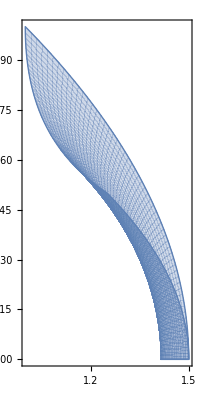

```mathematica
ParametricPlot[z0z4Figure5pt6 ,{x,1,2},{Subscript[η, 0],0,1},Mesh->False]
```

## Attempt at Visualization for Figures 5.7

```mathematica
Clear[hyperboloidFigure5pt7]
hyperboloidFigure5pt7 = 
eq5pt1 /. Subscript[Z, 2]-> 0 /. Subscript[Z, 3]-> 0 /. a-> 1
```

-Z_0^2+Z_1^2-Z_4^2==-1

```mathematica
(* Pick different mesh functions... *) 

ContourPlot3D[ Evaluate[hyperboloidFigure5pt7 ] , { Subscript[Z, 0] , -10 , 10 } , { Subscript[Z, 1] , -10 , 10 } , { Subscript[Z, 4] , -10 , 10 },MeshFunctions->{#1^2-#2^2&,#1^2+#3^2&}]
```

-Graphics3D-

```mathematica
eq5pt17[[1]] 
eq5pt17[[2]]
eq5pt17[[5]]
```

Z_0==a Sin[(t_-1)/a]

Z_1==a Cos[θ] Cos[(t_-1)/a] Sinh[ρ]

Z_4==a Cos[(t_-1)/a] Cosh[ρ]

```mathematica
Clear[z0z1z4Figure5pt7]
z0z1z4Figure5pt7 = {
Subscript[Z, 0] /. ( eq5pt17[[1]]  /. Equal-> Rule ) , 
Subscript[Z, 1] /. ( eq5pt17[[2]]  /. Equal-> Rule ) , 
Subscript[Z, 4] /.  ( eq5pt17[[5]]  /. Equal-> Rule )
} /. a-> 1 ;
z0z1z4Figure5pt7
```

{Sin[t_-1],Cos[θ] Cos[t_-1] Sinh[ρ],Cos[t_-1] Cosh[ρ]}

```mathematica
Clear[z0z1z4Figure5pt7b]
z0z1z4Figure5pt7b = {
Subscript[Z, 1] /. ( eq5pt17[[2]]  /. Equal-> Rule ) , 
Subscript[Z, 4] /.  ( eq5pt17[[5]]  /. Equal-> Rule )
} /. a-> 1 ;
z0z1z4Figure5pt7b
```

{Cos[θ] Cos[t_-1] Sinh[ρ],Cos[t_-1] Cosh[ρ]}

```mathematica
z0z1z4Figure5pt7b   /. Subscript[t, -1]-> 0
```

{Cos[θ] Sinh[ρ],Cosh[ρ]}

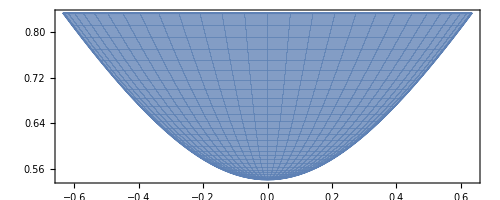

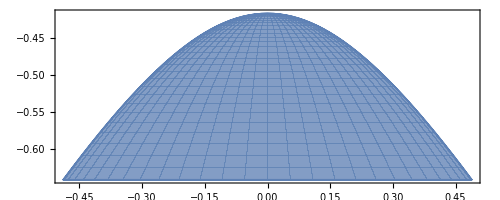

```mathematica
ParametricPlot[ Evaluate[z0z1z4Figure5pt7b   /. Subscript[t, -1]-> 1],{θ,0,2π},{ρ,-1,1}]
ParametricPlot[ Evaluate[z0z1z4Figure5pt7b   /. Subscript[t, -1]-> 2],{θ,0,2π},{ρ,-1,1}]
```